```mathematica
Clear[g];
```

## Version sin |-3>

```mathematica
V = g/2{{1,1},{√2,-√2}};
Hg = {{Ω,0},{0,0}};
Ematrix = {{Ω/2,0},{0,Ω/2}};
inv = Inverse[Ematrix-Hg];
```

```mathematica
heff =( V.inv.Vᵀ);
```

```mathematica
MatrixForm[heff]
```

(0 | -(√2 g^2)/Ω
-(√2 g^2)/Ω | 0)

```mathematica
H0 = {{Ω/2,0},{0,2Δa-Ω/2}}
```

{{Ω/2,0},{0,2 Δa-Ω/2}}

## Version sin |-3>

```mathematica
V = g/2{{1,1,0},{√2,-√2,-√3}};
Hg = {{Ω,0,0},{0,0,0},{0,0,Ω}};
Ematrix = {{Ω/2,0,0},{0,Ω/2,0},{0,0,Ω/2}};
inv = Inverse[Ematrix-Hg];
```

```mathematica
heff =( V.inv.Vᵀ);
```

```mathematica
MatrixForm[heff]
```

(0 | -(√2 g^2)/Ω
-(√2 g^2)/Ω | -(3 g^2)/(2 Ω))

```mathematica
H0 = {{Ω/2,0},{0,2Δa-Ω/2}}
```

{{Ω/2,0},{0,2 Δa-Ω/2}}

```mathematica
H=(H0 + heff)
```

{{Ω/2,-(√2 g^2)/Ω},{-(√2 g^2)/Ω,2 Δa-(3 g^2)/(2 Ω)-Ω/2}}

```mathematica
FullSimplify@Solve[2 Δa-(3 g^2)/(2 Ω)-Ω/2==Ω/2,{Δa}]
```

{{Δa→(3 g^2)/(4 Ω)+Ω/2}}

```mathematica
(3 g^2)/(4 Ω)/.{g->0.2, Ω->10}
```

0.003

```mathematica
U = MatrixExp[-ⅈ H t];
```

```mathematica
plus0 = {1,0};
```

```mathematica
ψt = U.plus0;
```

```mathematica
Ωsel = 10.;
gsel = 0.2;

ProbPlus0=Abs[ψt[[1]]]^2/.{Ω->Ωsel, g->gsel};
```

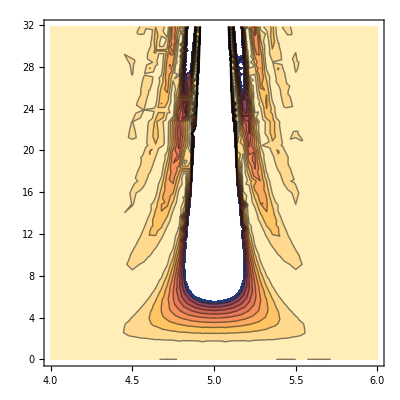

```mathematica
ContourPlot[ProbPlus0,{Δa,Ωsel/2-1.,Ωsel/2+1},{t,0,2000/(2 π Ωsel)}]
```